```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
boxLength=40;
```

```mathematica
Manipulate[
data=Import["data/lattice_v"<>IntegerString[iLatt,10,3]<>"/lattice/"<>IntegerString[t,10,4]<>".txt","Table"];
dataX=Select[data,#[[3]]=="X"&][[;;,{1,2}]];
dataY=Select[data,#[[3]]=="Y"&][[;;,{1,2}]];
dataX2=ConstantArray[0,{boxLength,boxLength}];
dataY2=ConstantArray[0,{boxLength,boxLength}];
Do[
dataX2[[pt[[1]],pt[[2]]]]=1;
,{pt,dataX}];
Do[
dataY2[[pt[[1]],pt[[2]]]]=1;
,{pt,dataY}];
ArrayPlot[dataX2]
,{t,0,500-1,1},{iLatt,1,10,1}]
```

Import::nffil: File data/lattice_v010/lattice/0499.txt not found during Import.

Select::normal: Nonatomic expression expected at position 1 in Select[$Failed,#1⟦3⟧==X&].

Part::partd: Part specification Select[$Failed,#1⟦3⟧==X&]⟦1;;All,{1,2}⟧ is longer than depth of object.

Select::normal: Nonatomic expression expected at position 1 in Select[$Failed,#1⟦3⟧==Y&].

Part::partd: Part specification Select[$Failed,#1⟦3⟧==Y&]⟦1;;All,{1,2}⟧ is longer than depth of object.

Part::partd: Part specification Select[$Failed,#1⟦3⟧==X&]⟦1;;All,{1,2}⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Do::iterb: Iterator {pt,dataX} does not have appropriate bounds.

Do::iterb: Iterator {pt,dataY} does not have appropriate bounds.

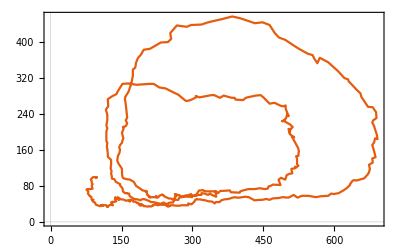
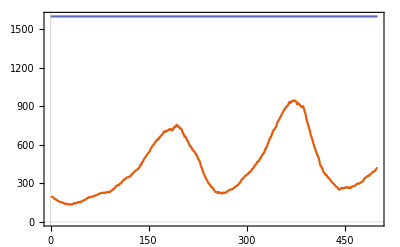

```mathematica
iLatt=20;
countsX=Import["data/lattice_v"<>IntegerString[iLatt,10,3]<>"/counts/X.txt","Table"];
countsY=Import["data/lattice_v"<>IntegerString[iLatt,10,3]<>"/counts/Y.txt","Table"];
sum=countsX[[;;,2]]+countsY[[;;,2]];
Row[{
ListLinePlot[Transpose[{countsX[[;;,2]],countsY[[;;,2]]}]],
ListLinePlot[{sum,{{0,1600},{500,1600}}},PlotRange->All]
}]
```

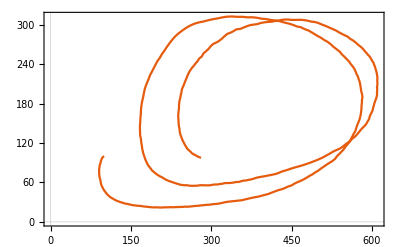

```mathematica
iLattStart=1;
iLattEnd=100;
countsX={};
countsY={};
Do[
countsXtmp=Import["data/lattice_v"<>IntegerString[iLatt,10,3]<>"/counts/X.txt","Table"];
countsYtmp=Import["data/lattice_v"<>IntegerString[iLatt,10,3]<>"/counts/Y.txt","Table"];
If[countsXtmp[[-1,2]]≠0&&countsYtmp[[-1,2]]≠0,
AppendTo[countsX,countsXtmp];
AppendTo[countsY,countsYtmp];
,
Print["Not: "<>ToString[iLatt]];
];
,{iLatt,iLattStart,iLattEnd}];
countsX=Mean[countsX]//N;
countsY=Mean[countsY]//N;
ListLinePlot[Transpose[{countsX[[;;,2]],countsY[[;;,2]]}]]
```